# Training data generation and state classification

## [1] Generalized Gell-Mann matrix basis

Function that generates a generalized Gell-Mann matrix basis (GGMMB) for an arbitrary N-level system. The(N^2-1)matrices/generators are stored in the list “MB”, and their N eigenvalues and N projectors are stored in the lists “EV” and “MBP”, respectively.

```mathematica
GGMMB[𝒩_]:=Module[{},Subscript[M, 1]=1/(√2)Flatten[Table[SparseArray[{{𝓆,𝓆𝓆}->I,{𝓆𝓆,𝓆}->I},{𝒩,𝒩}],{𝓆,1,𝒩},{𝓆𝓆,𝓆+1,𝒩}],1];Subscript[M, 2]=1/(√2)Flatten[Table[SparseArray[{{𝓆,𝓆𝓆}->-1,{𝓆𝓆,𝓆}->1},{𝒩,𝒩}],{𝓆,1,𝒩},{𝓆𝓆,𝓆+1,𝒩}],1];Subscript[M, 3]=Map[Composition[DiagonalMatrix,SparseArray],Orthogonalize[Table[SparseArray[{{𝓆}->I,{𝓆+1}->-I},𝒩],{𝓆,1,𝒩-1}]]];MB=(-I)Join[Subscript[M, 1],Subscript[M, 2],Subscript[M, 3]];
EV=Table[Eigenvalues[MB[[𝓆]]],{𝓆,1,𝒩^2-1}];
MBP=Table[Outer[Times,Map[Normalize,Eigenvectors[MB[[𝓆]]]][[𝓆𝓆]],Conjugate[Map[Normalize,Eigenvectors[MB[[𝓆]]]][[𝓆𝓆]]]],{𝓆,1,𝒩^2-1},{𝓆𝓆,1,𝒩}];];
```

## [2] Probability tuples and NM breakdown measure γ

Note: The file “ProbabilityTuples.nb” provides a graphical overview of the underlying probability distributions.

Probability tuples for NM-conforming states

```mathematica
NMcPT[𝒩_]:=Module[{list=RandomReal[{0,1},𝒩]},list/Total[list]];
```

Probability tuples for NM-violating states

```mathematica
NMvPT[𝒩_]:=Module[{list=RandomReal[{-1,1},𝒩-1]},last=1-Total[list];Flatten[{list,last}]];
```

Function that computes the NM breakdown measure γ for a given vector pvec

```mathematica
γ[pvec_]:=Total[Abs[Select[pvec,#<0&]]];
```

## [3] Training data generation

Function that generates 𝓃 NM-conforming probability vectors for an arbitrary N-level system.

```mathematica
NMcTDG[𝒩_,𝓃_]:=With[{𝒾=𝓃},
GGMMB[𝒩];
While[𝒿<𝒾,
pc=NMcPT[𝒩];
rv=RandomReal[{0,1},{𝒩,𝒩}];
v=Orthogonalize[rv,Method->"GramSchmidt"];
ρNMc=Sum[pc[[j]]Outer[Times,v[[j]],v[[j]]],{j,1,𝒩}];
pNMc=Chop[Flatten[Table[Tr[MBP[[i]][[j]].ρNMc],{i,1,𝒩^2-1},{j,1,𝒩}]]];
AppendTo[NMcList,{pc,ρNMc,pNMc}];
𝒿++
]
];
```

Function that generates 𝓃 NM-violating probability vectors for an arbitrary N-level system.

```mathematica
NMvTDG[𝒩_,𝓃_]:=With[{𝒾=𝓃},
GGMMB[𝒩];
While[Length[NMvList]<𝒾,
pv=NMvPT[𝒩];
rv=RandomReal[{0,1},{𝒩,𝒩}];
v=Orthogonalize[rv,Method->"GramSchmidt"];
ρNMv=Sum[pv[[j]]Outer[Times,v[[j]],v[[j]]],{j,1,𝒩}];
pNMv=Chop[Flatten[Table[Tr[MBP[[i]][[j]].ρNMv],{i,1,𝒩^2-1},{j,1,𝒩}]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],AppendTo[NMvList,{pv,ρNMv,pNMv}]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.1𝒾,Print["10%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.2𝒾,Print["20%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.3𝒾,Print["30%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.4𝒾,Print["40%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.5𝒾,Print["50%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.6𝒾,Print["60%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.7𝒾,Print["70%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.8𝒾,Print["80%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
If[NonNegative[Min[pNMv]&&Negative[Min[pv]]],If[Length[NMvList]==0.9𝒾,Print["90%, Vectors generated:",𝒸ℴ𝓊𝓃𝓉]]];
𝒸ℴ𝓊𝓃𝓉+=1;
𝒿++
]
];
```

Note: For large N it is more efficient to append only the relevant data (e.g. “pv”), but this shall not concern us here.

Note: The counter “𝒸ℴ𝓊𝓃𝓉” counts the total number of vectors that have been generated, including those associated with states that do not satisfy the second requirement in Eq. (5.1) of arXiv:2312.16281, which are discarded. As the histogram data generation in [4.1] below illustrates, the efficiency decreases sharpy with increasing N.

## Examples

#### N=2 [NMc]

Generate 10 NM-conforming probability vectors for N=2.

```mathematica
NMcList={};𝒿=0;
```

```mathematica
NMcTDG[2,10]
```

Display the generated probability tuples, density matrices, and probability vectors:

```mathematica
Table[NMcList[[i]]//MatrixForm,{i,1,Length[NMcList]}]
```

{({0.49359,0.50641}
{{0.498601,-0.0062559},{-0.0062559,0.501399}}
{0.506256,0.493744,0.5,0.5,0.501399,0.498601}),({0.611173,0.388827}
{{0.589253,0.0662819},{0.0662819,0.410747}}
{0.433718,0.566282,0.5,0.5,0.410747,0.589253}),({0.255485,0.744515}
{{0.693289,-0.149757},{-0.149757,0.306711}}
{0.649757,0.350243,0.5,0.5,0.306711,0.693289}),({0.419321,0.580679}
{{0.460775,-0.0705018},{-0.0705018,0.539225}}
{0.570502,0.429498,0.5,0.5,0.539225,0.460775}),({0.88489,0.11511}
{{0.148132,0.155979},{0.155979,0.851868}}
{0.344021,0.655979,0.5,0.5,0.851868,0.148132}),({0.257168,0.742832}
{{0.349451,-0.190532},{-0.190532,0.650549}}
{0.690532,0.309468,0.5,0.5,0.650549,0.349451}),({0.886151,0.113849}
{{0.684265,0.339351},{0.339351,0.315735}}
{0.160649,0.839351,0.5,0.5,0.315735,0.684265}),({0.386423,0.613577}
{{0.459643,-0.106165},{-0.106165,0.540357}}
{0.606165,0.393835,0.5,0.5,0.540357,0.459643}),({0.845154,0.154846}
{{0.555522,0.340659},{0.340659,0.444478}}
{0.159341,0.840659,0.5,0.5,0.444478,0.555522}),({0.372197,0.627803}
{{0.606125,-0.0712117},{-0.0712117,0.393875}}
{0.571212,0.428788,0.5,0.5,0.393875,0.606125})}

#### N=2 [NMv]

Generate 10 NM-violating probability vectors for N=2.

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
```

```mathematica
NMvTDG[2,10]
```

```mathematica
𝒸ℴ𝓊𝓃𝓉
```

434

Display the generated probability tuples, density matrices, and probability vectors:

```mathematica
Table[NMvList[[i]]//MatrixForm,{i,1,Length[NMvList]}]
```

{({-0.155476,1.15548}
{{0.971031,-0.455827},{-0.455827,0.028969}}
{0.955827,0.0441731,0.5,0.5,0.028969,0.971031}),({-0.0962775,1.09628}
{{0.898236,-0.443796},{-0.443796,0.101764}}
{0.943796,0.0562043,0.5,0.5,0.101764,0.898236}),({-0.0281864,1.02819}
{{0.177692,-0.418448},{-0.418448,0.822308}}
{0.918448,0.0815524,0.5,0.5,0.822308,0.177692}),({-0.0247614,1.02476}
{{0.687835,-0.489993},{-0.489993,0.312165}}
{0.989993,0.0100074,0.5,0.5,0.312165,0.687835}),({-0.0302017,1.0302}
{{0.735342,-0.475109},{-0.475109,0.264658}}
{0.975109,0.0248915,0.5,0.5,0.264658,0.735342}),({-0.0474219,1.04742}
{{0.23943,-0.481429},{-0.481429,0.76057}}
{0.981429,0.0185709,0.5,0.5,0.76057,0.23943}),({-0.0303469,1.03035}
{{0.8269,-0.417618},{-0.417618,0.1731}}
{0.917618,0.0823825,0.5,0.5,0.1731,0.8269}),({-0.0795095,1.07951}
{{0.926891,-0.391912},{-0.391912,0.0731088}}
{0.891912,0.108088,0.5,0.5,0.0731088,0.926891}),({-0.0236575,1.02366}
{{0.983215,-0.201794},{-0.201794,0.0167852}}
{0.701794,0.298206,0.5,0.5,0.0167852,0.983215}),({-0.155856,1.15586}
{{0.974127,-0.453157},{-0.453157,0.0258728}}
{0.953157,0.0468433,0.5,0.5,0.0258728,0.974127})}

Evaluate the degree of the NM violation:

```mathematica
Table[γ[γvecs[NMvList][[All,1]][[i]]],{i,1,Length[γvecs[NMvList][[All,1]]]}]
```

{0.155476,0.0962775,0.0281864,0.0247614,0.0302017,0.0474219,0.0303469,0.0795095,0.0236575,0.155856}

Sort from least to most NM-violating:

```mathematica
SortBy[%,Total]
```

{0.0236575,0.0247614,0.0281864,0.0302017,0.0303469,0.0474219,0.0795095,0.0962775,0.155476,0.155856}

#### N=3 [NMc]

Generate 10 NM-conforming probability vectors for N=3.

```mathematica
NMcList={};𝒿=0;
```

```mathematica
NMcTDG[3,10]
```

Show the generated probability tuples:

```mathematica
Table[NMcList[[i]][[1]]//MatrixForm,{i,1,Length[NMcList]}]
```

{(0.0389463
0.14913
0.811924),(0.299531
0.167612
0.532857),(0.285238
0.470559
0.244204),(0.378118
0.0860852
0.535797),(0.235471
0.30467
0.459859),(0.335155
0.105948
0.558897),(0.244884
0.33369
0.421426),(0.166885
0.14295
0.690164),(0.356335
0.547623
0.0960419),(0.226075
0.658645
0.11528)}

Or, alternatively:

```mathematica
NMcList[[All,1]]//MatrixForm
```

(0.0389463 | 0.14913 | 0.811924
0.299531 | 0.167612 | 0.532857
0.285238 | 0.470559 | 0.244204
0.378118 | 0.0860852 | 0.535797
0.235471 | 0.30467 | 0.459859
0.335155 | 0.105948 | 0.558897
0.244884 | 0.33369 | 0.421426
0.166885 | 0.14295 | 0.690164
0.356335 | 0.547623 | 0.0960419
0.226075 | 0.658645 | 0.11528)

Show the generated pseudo-density matrices:

```mathematica
Table[NMcList[[i]][[2]]//MatrixForm,{i,1,Length[NMcList]}]
```

{(0.378991 | 0.00246987 | -0.374647
0.00246987 | 0.138661 | -0.0579831
-0.374647 | -0.0579831 | 0.482348),(0.353243 | 0.0164524 | -0.0981093
0.0164524 | 0.169323 | -0.0167723
-0.0981093 | -0.0167723 | 0.477434),(0.298985 | -0.00934538 | -0.0477367
-0.00934538 | 0.250171 | 0.0350095
-0.0477367 | 0.0350095 | 0.450844),(0.296583 | -0.206737 | 0.0653245
-0.206737 | 0.356846 | 0.0633834
0.0653245 | 0.0633834 | 0.34657),(0.303797 | 0.0349865 | -0.0492422
0.0349865 | 0.41425 | -0.0672684
-0.0492422 | -0.0672684 | 0.281953),(0.383277 | -0.105073 | 0.0992425
-0.105073 | 0.474971 | -0.0278279
0.0992425 | -0.0278279 | 0.141752),(0.262264 | -0.0334151 | -0.0144254
-0.0334151 | 0.361139 | -0.0511785
-0.0144254 | -0.0511785 | 0.376597),(0.376746 | -0.0544483 | -0.255122
-0.0544483 | 0.171871 | 0.0815025
-0.255122 | 0.0815025 | 0.451383),(0.320822 | -0.0387546 | 0.191452
-0.0387546 | 0.409115 | -0.0909458
0.191452 | -0.0909458 | 0.270063),(0.217811 | 0.183577 | -0.060525
0.183577 | 0.467839 | -0.170813
-0.060525 | -0.170813 | 0.31435)}

Show the generated probability vectors:

```mathematica
Table[NMcList[[i]][[3]]//MatrixForm,{i,1,Length[NMcList]}]
```

{(0.256356
0.261296
0.482348
0.805316
0.0560226
0.138661
0.368487
0.252521
0.378991
0.258826
0.258826
0.482348
0.430669
0.430669
0.138661
0.310504
0.310504
0.378991
0.138661
0.378991
0.482348
0.482348
0.138661
0.378991),(0.24483
0.277735
0.477434
0.513448
0.317229
0.169323
0.340151
0.306606
0.353243
0.261283
0.261283
0.477434
0.415338
0.415338
0.169323
0.323379
0.323379
0.353243
0.169323
0.353243
0.477434
0.477434
0.169323
0.353243),(0.283923
0.265233
0.450844
0.422651
0.327178
0.250171
0.315498
0.385517
0.298985
0.274578
0.274578
0.450844
0.374914
0.374914
0.250171
0.350508
0.350508
0.298985
0.250171
0.298985
0.450844
0.450844
0.250171
0.298985),(0.533452
0.119978
0.34657
0.256252
0.386901
0.356846
0.288325
0.415092
0.296583
0.326715
0.326715
0.34657
0.321577
0.321577
0.356846
0.351708
0.351708
0.296583
0.356846
0.296583
0.34657
0.34657
0.356846
0.296583),(0.324037
0.39401
0.281953
0.342117
0.243633
0.41425
0.41537
0.280833
0.303797
0.359023
0.359023
0.281953
0.292875
0.292875
0.41425
0.348101
0.348101
0.303797
0.41425
0.303797
0.281953
0.281953
0.41425
0.303797),(0.534197
0.324051
0.141752
0.163272
0.361757
0.474971
0.336189
0.280533
0.383277
0.429124
0.429124
0.141752
0.262515
0.262515
0.474971
0.308361
0.308361
0.383277
0.474971
0.383277
0.141752
0.141752
0.474971
0.383277),(0.345116
0.278286
0.376597
0.333856
0.305005
0.361139
0.420047
0.31769
0.262264
0.311701
0.311701
0.376597
0.319431
0.319431
0.361139
0.368868
0.368868
0.262264
0.361139
0.262264
0.376597
0.376597
0.361139
0.262264),(0.328757
0.21986
0.451383
0.669186
0.158943
0.171871
0.230125
0.393129
0.376746
0.274309
0.274309
0.451383
0.414064
0.414064
0.171871
0.311627
0.311627
0.376746
0.171871
0.376746
0.451383
0.451383
0.171871
0.376746),(0.403723
0.326214
0.270063
0.10399
0.486894
0.409115
0.430535
0.248643
0.320822
0.364968
0.364968
0.270063
0.295442
0.295442
0.409115
0.339589
0.339589
0.320822
0.409115
0.320822
0.270063
0.270063
0.409115
0.320822),(0.159248
0.526402
0.31435
0.326606
0.205555
0.467839
0.561908
0.220281
0.217811
0.342825
0.342825
0.31435
0.26608
0.26608
0.467839
0.391094
0.391094
0.217811
0.467839
0.217811
0.31435
0.31435
0.467839
0.217811)}

#### N=3 [NMv]

Generate 10 NM-violating probability vectors for N=3.

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
```

```mathematica
NMvTDG[3,10]
```

```mathematica
𝒸ℴ𝓊𝓃𝓉
```

139

Show the generated probability tuples:

```mathematica
Table[NMvList[[i]][[1]]//MatrixForm,{i,1,Length[NMvList]}]
```

{(-0.0948295
0.0743982
1.02043),(-0.00875729
0.586198
0.42256),(0.374791
-0.0588485
0.684057),(0.662484
0.353929
-0.0164127),(-0.108319
0.374381
0.733938),(0.894825
-0.0855687
0.190743),(0.453624
0.559432
-0.0130563),(0.863873
-0.00125774
0.137385),(0.086316
0.923769
-0.0100847),(-0.0379139
0.433493
0.604421)}

Or, alternatively:

```mathematica
NMvList[[All,1]]//MatrixForm
```

(-0.0948295 | 0.0743982 | 1.02043
-0.00875729 | 0.586198 | 0.42256
0.374791 | -0.0588485 | 0.684057
0.662484 | 0.353929 | -0.0164127
-0.108319 | 0.374381 | 0.733938
0.894825 | -0.0855687 | 0.190743
0.453624 | 0.559432 | -0.0130563
0.863873 | -0.00125774 | 0.137385
0.086316 | 0.923769 | -0.0100847
-0.0379139 | 0.433493 | 0.604421)

Show the generated pseudo-density matrices:

```mathematica
Table[NMvList[[i]][[2]]//MatrixForm,{i,1,Length[NMvList]}]
```

{(0.847277 | -0.338399 | -0.203557
-0.338399 | 0.0268275 | 0.068784
-0.203557 | 0.068784 | 0.125896),(0.344145 | -0.00177687 | -0.210053
-0.00177687 | 0.493411 | -0.151215
-0.210053 | -0.151215 | 0.162444),(0.606704 | 0.170716 | -0.148035
0.170716 | 0.138752 | 0.169727
-0.148035 | 0.169727 | 0.254544),(0.411074 | 0.055358 | 0.250124
0.055358 | 0.404708 | 0.182292
0.250124 | 0.182292 | 0.184218),(0.432019 | -0.136414 | -0.331861
-0.136414 | 0.202125 | -0.189383
-0.331861 | -0.189383 | 0.365856),(0.528595 | 0.394208 | 0.0949423
0.394208 | 0.470227 | -0.0867769
0.0949423 | -0.0867769 | 0.00117724),(0.378518 | -0.00343856 | 0.175483
-0.00343856 | 0.55305 | -0.0416804
0.175483 | -0.0416804 | 0.0684319),(0.0256231 | 0.124502 | 0.0838011
0.124502 | 0.612826 | 0.326477
0.0838011 | 0.326477 | 0.361551),(0.0584549 | -0.170016 | 0.137011
-0.170016 | 0.677735 | -0.341474
0.137011 | -0.341474 | 0.26381),(0.402858 | -0.0339754 | -0.111819
-0.0339754 | 0.531281 | -0.198079
-0.111819 | -0.198079 | 0.0658609)}

Show the generated probability vectors:

```mathematica
Table[NMvList[[i]][[3]]//MatrixForm,{i,1,Length[NMvList]}]
```

{(0.775451
0.0986532
0.125896
0.690143
0.28303
0.0268275
0.00757773
0.145146
0.847277
0.437052
0.437052
0.125896
0.486586
0.486586
0.0268275
0.0763617
0.0763617
0.847277
0.0268275
0.847277
0.125896
0.125896
0.0268275
0.847277),(0.420555
0.417001
0.162444
0.463348
0.0432417
0.493411
0.479143
0.176712
0.344145
0.418778
0.418778
0.162444
0.253295
0.253295
0.493411
0.327927
0.327927
0.344145
0.493411
0.344145
0.162444
0.162444
0.493411
0.344145),(0.202012
0.543444
0.254544
0.578659
0.282589
0.138752
0.0269208
0.366376
0.606704
0.372728
0.372728
0.254544
0.430624
0.430624
0.138752
0.196648
0.196648
0.606704
0.138752
0.606704
0.254544
0.254544
0.138752
0.606704),(0.352533
0.463249
0.184218
0.0475225
0.54777
0.404708
0.112171
0.476755
0.411074
0.407891
0.407891
0.184218
0.297646
0.297646
0.404708
0.294463
0.294463
0.411074
0.404708
0.411074
0.184218
0.184218
0.404708
0.411074),(0.453486
0.180658
0.365856
0.730799
0.0670764
0.202125
0.473374
0.094607
0.432019
0.317072
0.317072
0.365856
0.398938
0.398938
0.202125
0.28399
0.28399
0.432019
0.202125
0.432019
0.365856
0.365856
0.202125
0.432019),(0.105203
0.89362
0.00117724
0.169944
0.359829
0.470227
0.322479
0.148925
0.528595
0.499411
0.499411
0.00117724
0.264886
0.264886
0.470227
0.235702
0.235702
0.528595
0.470227
0.528595
0.00117724
0.00117724
0.470227
0.528595),(0.469223
0.462345
0.0684319
0.0479923
0.398958
0.55305
0.352421
0.269061
0.378518
0.465784
0.465784
0.0684319
0.223475
0.223475
0.55305
0.310741
0.310741
0.378518
0.55305
0.378518
0.0684319
0.0684319
0.55305
0.378518),(0.194722
0.443727
0.361551
0.109786
0.277388
0.612826
0.160711
0.813666
0.0256231
0.319224
0.319224
0.361551
0.193587
0.193587
0.612826
0.487188
0.487188
0.0256231
0.612826
0.0256231
0.361551
0.361551
0.612826
0.0256231),(0.538111
0.198078
0.26381
0.0241217
0.298144
0.677735
0.812246
0.129299
0.0584549
0.368095
0.368095
0.26381
0.161133
0.161133
0.677735
0.470773
0.470773
0.0584549
0.677735
0.0584549
0.26381
0.26381
0.677735
0.0584549),(0.501045
0.433094
0.0658609
0.346178
0.122541
0.531281
0.49665
0.100492
0.402858
0.46707
0.46707
0.0658609
0.234359
0.234359
0.531281
0.298571
0.298571
0.402858
0.531281
0.402858
0.0658609
0.0658609
0.531281
0.402858)}

Evaluate the degree of the NM violation:

```mathematica
Table[γ[γvecs[NMvList][[All,1]][[i]]],{i,1,Length[γvecs[NMvList][[All,1]]]}]
```

{0.0948295,0.00875729,0.0588485,0.0164127,0.108319,0.0855687,0.0130563,0.00125774,0.0100847,0.0379139}

Sort from least to most NM-violating:

```mathematica
SortBy[%,Total]
```

{0.00125774,0.00875729,0.0100847,0.0130563,0.0164127,0.0379139,0.0588485,0.0855687,0.0948295,0.108319}

## [4] Evaluating the NM violation measure

## [4.1] Generating histogram data

#### Generate 100,000 NM-violating probability vectors for N=2

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[2,100000]]
Print["Total number of generated vectors: ", 𝒸ℴ𝓊𝓃𝓉]
N2NMvList=NMvList;
```

10%, Vectors generated:346985

20%, Vectors generated:694441

30%, Vectors generated:1043386

40%, Vectors generated:1395187

50%, Vectors generated:1744797

60%, Vectors generated:2086522

70%, Vectors generated:2432014

80%, Vectors generated:2773597

90%, Vectors generated:3119987

{226.219,Null}

Total number of generated vectors: 3469830

```mathematica
AbsoluteTiming[N2γs=Table[γ[N2NMvList[[All,1]][[i]]],{i,1,Length[N2NMvList]}];N2γmean=NumberForm[Mean[N2γs],4];]
```

{464.332,Null}

#### Generate 100,000 NM-violating probability vectors for N=3

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[3,100000]]
Print["Total number of generated vectors: ", 𝒸ℴ𝓊𝓃𝓉]
N3NMvList=NMvList;
```

10%, Vectors generated:196419

20%, Vectors generated:390632

30%, Vectors generated:581310

40%, Vectors generated:781515

50%, Vectors generated:977578

60%, Vectors generated:1173974

70%, Vectors generated:1367387

80%, Vectors generated:1568033

90%, Vectors generated:1763412

{279.662,Null}

Total number of generated vectors: 1958243

```mathematica
AbsoluteTiming[N3γs=Table[γ[N3NMvList[[All,1]][[i]]],{i,1,Length[N3NMvList]}];N3γmean=NumberForm[Mean[N3γs],4];]
```

{329.644,Null}

#### Generate 100,000 NM-violating probability vectors for N=4

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[4,100000]]
Print["Total number of generated vectors: ", 𝒸ℴ𝓊𝓃𝓉]
N4NMvList=NMvList;
```

10%, Vectors generated:484350

20%, Vectors generated:966342

30%, Vectors generated:1439530

40%, Vectors generated:1909474

50%, Vectors generated:2390484

60%, Vectors generated:2866180

70%, Vectors generated:3344062

80%, Vectors generated:3823974

90%, Vectors generated:4297901

{1154.9,Null}

Total number of generated vectors: 4773609

```mathematica
AbsoluteTiming[N4γs=Table[γ[N4NMvList[[All,1]][[i]]],{i,1,Length[N4NMvList]}];N4γmean=NumberForm[Mean[N4γs],4];]
```

{334.124,Null}

#### Generate 100,000 NM-violating probability vectors for N=6

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[6,100000]]
Print["Total number of generated vectors: ", 𝒸ℴ𝓊𝓃𝓉]
N6NMvList=NMvList;
```

10%, Vectors generated:9623137

20%, Vectors generated:19471278

30%, Vectors generated:29106932

40%, Vectors generated:38589715

50%, Vectors generated:48006158

60%, Vectors generated:57379267

70%, Vectors generated:66875179

80%, Vectors generated:76316206

90%, Vectors generated:85963790

{69850.,Null}

Total number of generated vectors: 95459668

```mathematica
AbsoluteTiming[N6γs=Table[γ[N6NMvList[[All,1]][[i]]],{i,1,Length[N6NMvList]}];N6γmean=NumberForm[Mean[N6γs],4];]
```

{398.595,Null}

#### Generate NM-violating probability vectors for N=7 [evaluation aborted due to long computation time]

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[7,100000]]
Print["Total number of generated vectors: ", 𝒸ℴ𝓊𝓃𝓉]
N7NMvList=NMvList;
```

$Aborted

Total number of generated vectors: 27019566

```mathematica
Length[NMvList]
```

4538

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["N7NMvList[4538].mx",NMvList];
```

```mathematica
AbsoluteTiming[N7γs=Table[γ[N7NMvList[[All,1]][[i]]],{i,1,Length[N7NMvList]}];N7γmean=NumberForm[Mean[N7γs],4];]
```

#### Export lists

```mathematica
SetDirectory[NotebookDirectory[]];
```

Export lists of γ values

```mathematica
Export["N2γs.mx",N2γs];
Export["N3γs.mx",N3γs];
Export["N4γs.mx",N4γs];
Export["N6γs.mx",N6γs];
```

Export master lists including all probability tuples, density operators, and state vectors
(Note: Large file sizes for large N)

```mathematica
Export["N2NMvList.mx",N2NMvList];
Export["N3NMvList.mx",N3NMvList];
Export["N4NMvList.mx",N4NMvList];
Export["N6NMvList.mx",N6NMvList];
```

## [4.2] Plotting histogram data

```mathematica
SetDirectory[NotebookDirectory[]];
```

Import lists of γ values for N ∈ {2,4,6}

```mathematica
N2γs=Import["N2γs.mx"];
N4γs=Import["N4γs.mx"];
N6γs=Import["N6γs.mx"];
```

Calculate mean γ values

```mathematica
N2γmean=NumberForm[Mean[N2γs],4];
N4γmean=NumberForm[Mean[N4γs],4];
N6γmean=NumberForm[Mean[N6γs],4];
```

Plot histogram data for N=2

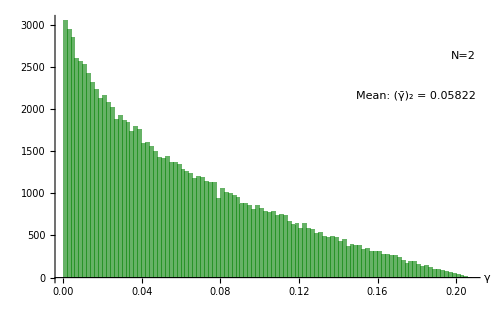

```mathematica
HistN2=Show[Histogram[N2γs,100,AxesLabel->{"StyleBox[\"γ\",FontFamily->\"Times New Roman\",FontSize->19,FontWeight->\"Regular\",FontSlant->\"Italic\"]",None},AxesStyle->{Arrowheads[{0,0.03}],Automatic},PlotRange->All,ChartStyle->{Opacity[0.6,Darker[Green,0.5]]}],LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->13,Black],Epilog->{Inset[Framed[Style["Mean:" ToExpression["\\overline\\gamma_2",TeXForm,HoldForm] Text["="N2γmean],14],RoundingRadius->2],Scaled[{0.85,0.70}]],Inset[Framed[Style["N=2",14],RoundingRadius->2],Scaled[{0.96,0.85}]]},ImagePadding->36,PlotRangeClipping->False,ImageSize->500]
```

Plot histogram data for N=4

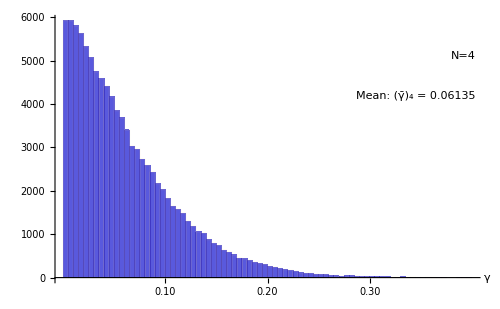

```mathematica
HistN4=Show[Histogram[N4γs,100,AxesLabel->{"StyleBox[\"γ\",FontFamily->\"Times New Roman\",FontSize->19,FontWeight->\"Regular\",FontSlant->\"Italic\"]",None},AxesStyle->{Arrowheads[{0,0.03}],Automatic},PlotRange->All,ChartStyle->{Opacity[0.65,Darker[Blue,0.2]]}],LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->13,Black],Ticks->{{{0.10,"0.10"},{0.20,"0.20"},{0.30,"0.30"}},Automatic},Epilog->{Inset[Framed[Style["Mean:" ToExpression["\\overline\\gamma_4",TeXForm,HoldForm] Text["="N4γmean],14],RoundingRadius->2],Scaled[{0.85,0.70}]],Inset[Framed[Style["N=4",14],RoundingRadius->2],Scaled[{0.96,0.85}]]},ImagePadding->36,PlotRangeClipping->False,ImageSize->500]
```

Plot histogram data for N=6

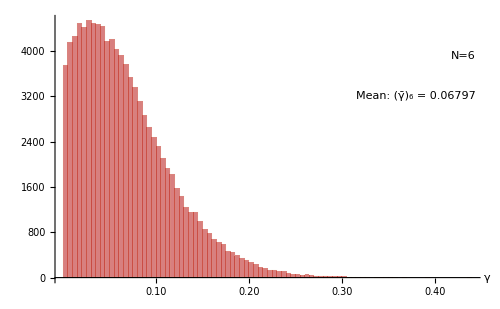

```mathematica
HistN6=Show[Histogram[N6γs,100,AxesLabel->{"StyleBox[\"γ\",FontFamily->\"Times New Roman\",FontSize->19,FontWeight->\"Regular\",FontSlant->\"Italic\"]",None},AxesStyle->{Arrowheads[{0,0.03}],Automatic},PlotRange->All,ChartStyle->{Opacity[0.5,Darker[Red,0.3]]}],LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->13,Black],Ticks->{{{0.10,"0.10"},{0.20,"0.20"},{0.30,"0.30"},{0.40,"0.40"}},Automatic},Epilog->{Inset[Framed[Style["Mean:" ToExpression["\\overline\\gamma_6",TeXForm,HoldForm] Text["="N6γmean],14],RoundingRadius->2],Scaled[{0.85,0.70}]],Inset[Framed[Style["N=6",14],RoundingRadius->2],Scaled[{0.96,0.85}]]},ImagePadding->36,PlotRangeClipping->False,ImageSize->500]
```

Plot histogram data for N ∈ {2,4,6} in a single histogram

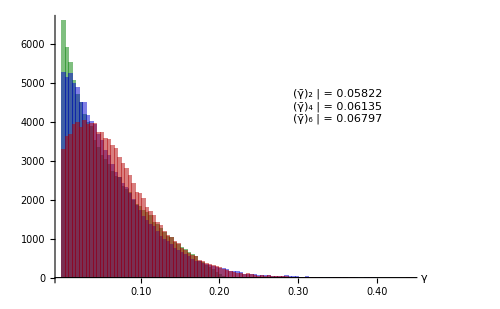

```mathematica
HistN246=Histogram[{N2γs,N4γs,N6γs},{"Raw",100},ChartStyle->{Darker[Green,0.5],Darker[Blue,0.2],Darker[Red,0.3]},PlotRange->All,AxesLabel->{"StyleBox[\"γ\",FontFamily->\"Times New Roman\",FontSize->19,FontWeight->\"Regular\",FontSlant->\"Italic\"]",None},AxesStyle->{Arrowheads[{0,0.02}],Automatic},LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->13,Black],Ticks->{{{0.10,"0.10"},{0.20,"0.20"},{0.30,"0.30"},{0.40,"0.40"}},Automatic},ImageSize->500,Epilog->Inset[Framed[SwatchLegend[{Darker[Green,0.5],Darker[Blue,0.2],Darker[Red,0.3]},{Style["N=2",15],Style["N=4",15],Style["N=6",15]},LegendMarkerSize->{14,14}]Grid[{{Style[ToExpression["\\overline\\gamma_2",TeXForm,HoldForm],14],Style["="N2γmean,14]},{Style[ToExpression["\\overline\\gamma_4",TeXForm,HoldForm],14],Style["="N4γmean,14]},{Style[ToExpression["\\overline\\gamma_6",TeXForm,HoldForm],14],Style["="N6γmean,14]}},Alignment->Left],RoundingRadius->1],Scaled[{0.78,0.66}]]]
```

Fig. 2 of arXiv:2312.16281 [quant-ph]

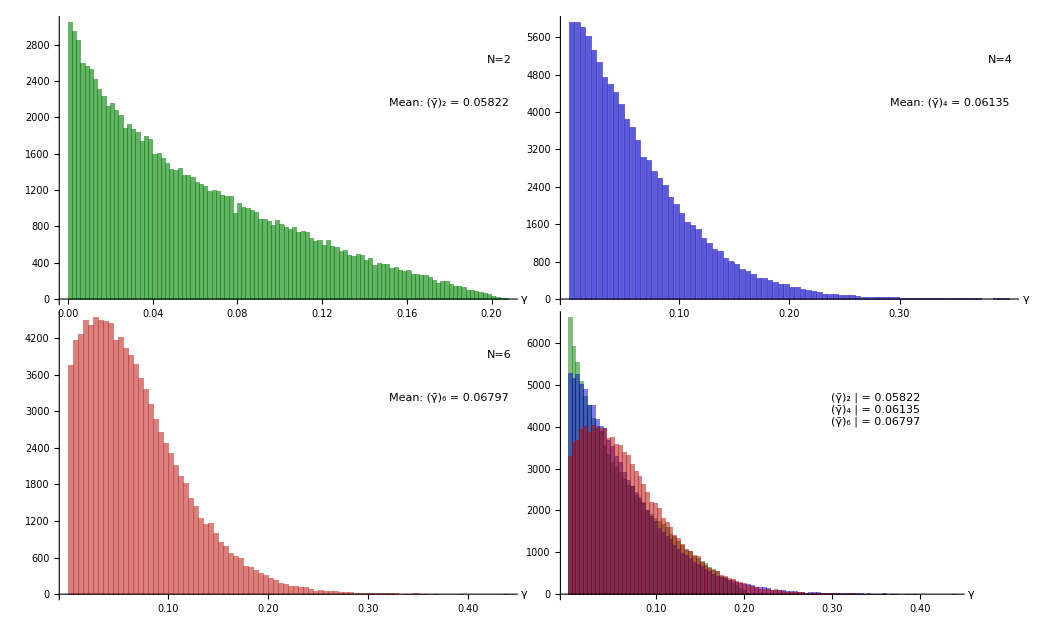

```mathematica
GraphicsGrid[{{HistN2,HistN4},{HistN6,HistN246}},ImageSize->1040,Spacings->-35]
```

## [5] State classification with machine learning

## [N=2] (500,000) Single-qubit system

Generate 500,000 NM-conforming probability vectors for N=2

```mathematica
NMcList={};𝒿=0;
AbsoluteTiming[NMcTDG[2,500000]]
N2NMcML=NMcList;
```

{3588.39,Null}

Generate 500,000 NM-violating probability vectors for N=2

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[2,500000]]
𝒸ℴ𝓊𝓃𝓉
N2NMvML=NMvList;
```

{3563.55,Null}

17420571

Export the generated lists

```mathematica
SetDirectory[NotebookDirectory[]];
Export["N2NMcML.mx",N2NMcML];
Export["N2NMvML.mx",N2NMvML];
```

Store the corresponding probability vectors in a separate list

```mathematica
N2NMcMLpvec=N2NMcML[[All,3]];
N2NMvMLpvec=N2NMvML[[All,3]];
```

Assign the value 0 [1] to vectors from the NM-conforming [NM-violating] data set, then join the two lists. The resulting list is the training data for the classifier function.

```mathematica
N2NMcMLpvecTD=Table[N2NMcMLpvec[[i]]->0,{i,1,Length[N2NMcMLpvec]}];
N2NMvMLpvecTD=Table[N2NMvMLpvec[[i]]->1,{i,1,Length[N2NMvMLpvec]}];
N2MLTD=Join[N2NMcMLpvecTD,N2NMvMLpvecTD];
```

Train a classifier function based on the training data (i.e. the joined list)

```mathematica
AbsoluteTiming[C2=Classify[N2MLTD]]
```

{49.5151,ClassifierFunction[…]}

Export the classifier function

```mathematica
Export["C2[0.5m].wmlf",C2]
```

C2[0.5m].wmlf

Check classification of state from the NM-conforming data set:

```mathematica
N2NMcMLpvec[[1]]
```

{0.806485,0.193515,0.5,0.5,0.502573,0.497427}

```mathematica
C2[N2NMcMLpvec[[1]]]
```

0

Check classification of state from the NM-violating data set:

```mathematica
N2NMvMLpvec[[1]]
```

{0.996329,0.00367117,0.5,0.5,0.339452,0.660548}

```mathematica
C2[N2NMvMLpvec[[1]]]
```

1

We can check that this state lies outside of the Bloch sphere to confirm its classification as NM-violating:

```mathematica
(N2NMvMLpvec[[1]][[1]]-N2NMvMLpvec[[1]][[2]])^2+(N2NMvMLpvec[[1]][[5]]-N2NMvMLpvec[[1]][[6]])^2
```

1.08847

If we slightly adjust its components such that it satisfies the Bloch sphere defining inequality, the classifier will correctly identify it as NM-conforming:

```mathematica
(0.9663288288257757-0.0336711711742245523)^2+(0.3394517022179654-0.6605482977820348)^2
```

0.972953

```mathematica
C2[{0.9663288288257757,0.0336711711742245523,0.5000000000000001,0.5000000000000001,0.3394517022179654,0.6605482977820348}]
```

0

## [N=3] (500,000)

The code for N=3 works analogous to the code for N=2. Note that the input for the classifier function is now a 24-dimensional vector (as opposed to 6-dimensional for N=2).

```mathematica
NMcList={};𝒿=0;
AbsoluteTiming[NMcTDG[3,500000]]
N3NMcML=NMcList;
```

{3500.76,Null}

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[3,500000]]
𝒸ℴ𝓊𝓃𝓉
N3NMvML=NMvList;
```

{4037.4,Null}

9782103

```mathematica
SetDirectory[NotebookDirectory[]];
Export["N3NMcML.mx",N3NMcML];
Export["N3NMvML.mx",N3NMvML];
```

```mathematica
N3NMcMLpvec=N3NMcML[[All,3]];
N3NMvMLpvec=N3NMvML[[All,3]];
```

```mathematica
N3NMcMLpvecTD=Table[N3NMcMLpvec[[i]]->0,{i,1,Length[N3NMcMLpvec]}];
N3NMvMLpvecTD=Table[N3NMvMLpvec[[i]]->1,{i,1,Length[N3NMvMLpvec]}];
N3MLTD=Join[N3NMcMLpvecTD,N3NMvMLpvecTD];
```

```mathematica
AbsoluteTiming[C3=Classify[N3MLTD]]
```

{60.0324,ClassifierFunction[…]}

```mathematica
Export["C3[0.5m].wmlf",C3]
```

C3[0.5m].wmlf

## [N=4] (500,000)

The code for N=4 works analogous to the code above. Note that the input for the classifier function is now a 60-dimensional vector.

```mathematica
NMcList={};𝒿=0;
AbsoluteTiming[NMcTDG[4,500000]]
N4NMcML=NMcList;
```

{3788.27,Null}

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[4,500000]]
𝒸ℴ𝓊𝓃𝓉
N4NMvML=NMvList;
```

{8330.47,Null}

23772427

```mathematica
SetDirectory[NotebookDirectory[]];
Export["N4NMcML.mx",N4NMcML];
Export["N4NMvML.mx",N4NMvML];
```

```mathematica
N4NMcMLpvec=N4NMcML[[All,3]];
N4NMvMLpvec=N4NMvML[[All,3]];
```

```mathematica
N4NMcMLpvecTD=Table[N4NMcMLpvec[[i]]->0,{i,1,Length[N4NMcMLpvec]}];
N4NMvMLpvecTD=Table[N4NMvMLpvec[[i]]->1,{i,1,Length[N4NMvMLpvec]}];
N4MLTD=Join[N4NMcMLpvecTD,N4NMvMLpvecTD];
```

```mathematica
AbsoluteTiming[C4=Classify[N4MLTD]]
```

{297.831,ClassifierFunction[…]}

```mathematica
Export["C4[0.5m].wmlf",C4]
```

C4[0.5m].wmlf

## [N=5] (500,000)

The code for N=4 works analogous to the code above. Note that the input for the classifier function is now a 120-dimensional vector.

```mathematica
NMcList={};𝒿=0;
AbsoluteTiming[NMcTDG[5,500000]]
N5NMcML=NMcList;
```

{3845.9,Null}

```mathematica
NMvList={};𝒿=0;𝒸ℴ𝓊𝓃𝓉=0;
AbsoluteTiming[NMvTDG[5,500000]]
𝒸ℴ𝓊𝓃𝓉
N5NMvML=NMvList;
```

{40651.8,Null}

92760173

```mathematica
SetDirectory[NotebookDirectory[]];
Export["N5NMcML.mx",N5NMcML];
Export["N5NMvML.mx",N5NMvML];
```

```mathematica
N5NMcMLpvec=N5NMcML[[All,3]];
N5NMvMLpvec=N5NMvML[[All,3]];
```

```mathematica
N5NMcMLpvecTD=Table[N5NMcMLpvec[[i]]->0,{i,1,Length[N5NMcMLpvec]}];
N5NMvMLpvecTD=Table[N5NMvMLpvec[[i]]->1,{i,1,Length[N5NMvMLpvec]}];
N5MLTD=Join[N5NMcMLpvecTD,N5NMvMLpvecTD];
```

```mathematica
AbsoluteTiming[C5=Classify[N5MLTD]]
```

{410.05,ClassifierFunction[…]}

```mathematica
Export["C5[0.5m].wmlf",C5]
```

C5[0.5m].wmlf